```mathematica
Clear[axk,ayk,k,ax,ay,bx,by,qx,qy]
```

#### Using the Bouwkamp definition for impedance; Power/v^2 Power emitted by the radiator at z=0 plane is the integral of p(x,y)*v(x,y) ds over x-y plane leads to the square of the fourier transform of the deflection profile in the integrand = S^2(kx,ax,bx) * S^2(ky,ay,by) where S(k,a,b) is 1D FT of one of the dimensions of the deflection profile - defined in the notes S(kx,ax,bx)/bx = xS below; q=a/b

```mathematica
xS=((-8/x)((1/(x^2) + 6/(x^4) + (2/5)*(SphericalBesselY[3,x]+SphericalBesselY[1,x]))*Sin[qx*x] + (-2/5)*(SphericalBesselJ[3,x] + SphericalBesselJ[1,x])*Cos[qx*x]))^2;
```

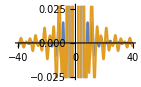
```mathematica
(*qx=1;
Plot[{xS[x,qx], 3.0671312295349495 Sinc[1.5355271144573683 x] Sinc[0.37611190490493007 x]},{x,-40,40}]*)
-Graphics-
(*
Clear[a,b,qx]
qx=1;
pnts=Table[{x,Re[xS[x,qx]]},{x,-5,5,0.015}]//N;
ListPlot[%]
FindFit[pnts,a Sinc[b x] Sinc[d x],{a,b,c,d},x]
(*
Table[{qx,FindFit[Table[Re[xS[x,qx]],{x,-5,5,0.015}]//N,a Sinc[b x],{a,b},x]},{qx,{1,2,3,4,5,6,7,8,9,10}}]*)*)
-Graphics-
{a->3.0671312295349495,b->1.5355271144573683,c->1.,d->0.37611190490493007}
```

Using the first identity listed here: https://dlmf.nist.gov/10.51
The following is equivalent to the expression above

```mathematica
xSs=(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2;
(*qx=2;
NIntegrate[Abs[xS-xSs],{x,-50,50}]
Plot[{xS,xSs},{x,-5,5}]*)
```

64 (-2/5 Cos[qx x] (1/3 SphericalBesselJ[0,x]+10/21 SphericalBesselJ[2,x]+1/7 SphericalBesselJ[4,x])+Sin[qx x] (6/x^5+1/x^3+2/5 (1/3 SphericalBesselY[0,x]+10/21 SphericalBesselY[2,x]+1/7 SphericalBesselY[4,x])))^2

The impedance is then the integral of “S^2(kx,ax,bx) S^2(ky,ay,by) 1/kz dkx dky“ over kx and ky from -inf to inf
with the coefficient \frac{k\rho c v^2_0 }{4\pi^2} b^2_x b^2_y
	After change of variables the integrand will be: “S^2(k t cos(phi),ax,bx) S^2(k t sin(phi),ay,by) t dt dphi / sqrt(1-t^2)”
	with the coefficient: \frac{k^2 \rho c v^2_0 }{4\pi^2} b^2_x b^2_y * (1/V_ref)^2

```mathematica
xOrig=(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2
xOrig=ReplaceAll[xOrig,x->(bxk*t*Cos[ϕ])];
yOrig=(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2;
yOrig=ReplaceAll[yOrig,qx->qy];
yOrig=ReplaceAll[yOrig,x->(byk*t*Sin[ϕ])];
```

64 (-2/5 Cos[qx x] (1/3 SphericalBesselJ[0,x]+10/21 SphericalBesselJ[2,x]+1/7 SphericalBesselJ[4,x])+Sin[qx x] (6/x^5+1/x^3+2/5 (1/3 SphericalBesselY[0,x]+10/21 SphericalBesselY[2,x]+1/7 SphericalBesselY[4,x])))^2

```mathematica
Series[(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2,{x,0,8}]
```

4/225 (8+15 qx)^2-(4 ((8+15 qx) (8+35 qx+56 qx^2+35 qx^3)) x^2)/1575+64 (((8+35 qx+56 qx^2+35 qx^3)^2)/705600+2 (-2/15-qx/4) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) x^4+64 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-2/15-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))) x^6+64 ((-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-2/15-qx/4) (-qx/2419200-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) x^8+O[x]^9

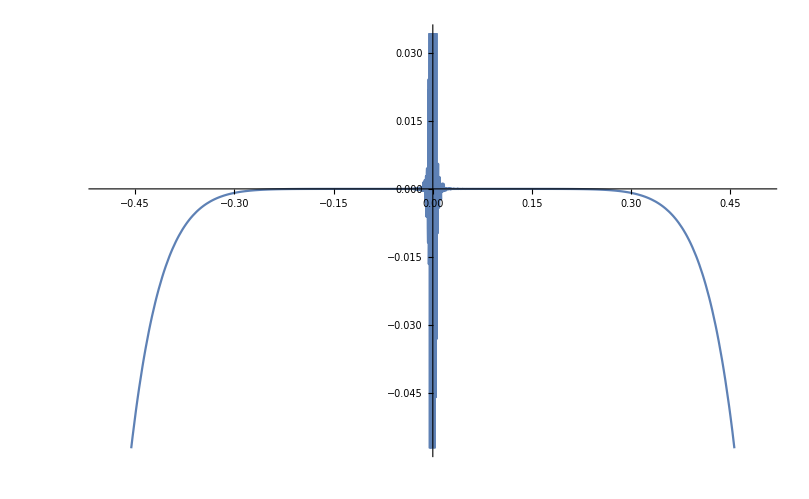

```mathematica
qx=2;
tempo=(-8((1/(x^3) + 6/(x^5) + (2/5)*((1/3)SphericalBesselY[0,x]+(10/21)SphericalBesselY[2,x]+(1/7)SphericalBesselY[4,x]))*Sin[qx*x] + (-2/5)*((1/3)SphericalBesselJ[0,x]+(10/21)SphericalBesselJ[2,x]+(1/7)SphericalBesselJ[4,x])*Cos[qx*x]))^2;
tempx=4/225 (8+15 qx)^2-(4 ((8+15 qx) (8+35 qx+56 qx^2+35 qx^3)) x^2)/1575+64 (((8+35 qx+56 qx^2+35 qx^3)^2)/705600+2 (-2/15-qx/4) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) x^4+64 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-2/15-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))) x^6+64 ((-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-2/15-qx/4) (-qx/2419200-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) x^8;
Plot[{100*tempo-100*tempx},{x,-0.5,0.5}]
```

```mathematica
xApprox=4/225 (8+15 qx)^2-(4 ((8+15 qx) (8+35 qx+56 qx^2+35 qx^3)) x^2)/1575+64 (((8+35 qx+56 qx^2+35 qx^3)^2)/705600+2 (-2/15-qx/4) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) x^4+64 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-2/15-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))) x^6+64 ((-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-2/15-qx/4) (-qx/2419200-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) x^8;
(*xApprox=ReplaceAll[xApprox,qx->(ax/bx)];*)
xApprox=ReplaceAll[xApprox,x->(bxk*t*Cos[ϕ])];

yApprox=4/225 (8+15 qx)^2-(4 ((8+15 qx) (8+35 qx+56 qx^2+35 qx^3)) x^2)/1575+64 (((8+35 qx+56 qx^2+35 qx^3)^2)/705600+2 (-2/15-qx/4) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) x^4+64 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-2/15-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))) x^6+64 ((-qx/576-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-1/99792-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-2/15-qx/4) (-qx/2419200-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) x^8;
(*yApprox=ReplaceAll[yApprox,qx->(ay/by)];*)
yApprox=ReplaceAll[yApprox,qx->qy];
yApprox=ReplaceAll[yApprox,x->(byk*t*Sin[ϕ])];
```

4/225 (8+15 qy)^2-(4 byk^2 (8+15 qy) (8+35 qy+56 qy^2+35 qy^3) t^2 Sin[ϕ]^2)/1575+64 byk^4 (((8+35 qy+56 qy^2+35 qy^3)^2)/705600+2 (-2/15-qy/4) (-qy/576-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))) t^4 Sin[ϕ]^4+64 byk^6 (1/420 (8+35 qy+56 qy^2+35 qy^3) (-qy/576-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))+2 (-2/15-qy/4) (qy/28800+qy^3/3456+qy^5/2880+qy^7/20160-2/5 (-1/99792-qy^2/3024-qy^4/1008-qy^6/2160))) t^6 Sin[ϕ]^6+64 byk^8 ((-qy/576-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))^2+1/420 (8+35 qy+56 qy^2+35 qy^3) (qy/28800+qy^3/3456+qy^5/2880+qy^7/20160-2/5 (-1/99792-qy^2/3024-qy^4/1008-qy^6/2160))+2 (-2/15-qy/4) (-qy/2419200-qy^3/172800-qy^5/69120-qy^7/120960-qy^9/1451520-2/5 (1/10378368+qy^2/199584+qy^4/36288+qy^6/30240+qy^8/120960))) t^8 Sin[ϕ]^8

```mathematica
(*axk=1;
ayk=1;
ax=0.003;
ay=0.003;
k=axk/ax;
bx=0.5/k;
by=0.5/k;*)
```

```mathematica
xComplete=Piecewise[{{xApprox,Abs[bxk t Cos[ϕ]]<0.1}},xOrig];
yComplete=Piecewise[{{yApprox,Abs[byk t Sin[ϕ]]<0.1}},yOrig];
```

```mathematica
3600 k^2 *(((ax+bx)^2)/(15 ax+8 bx))*(((ay+by)^2)/(15 ay+8 by))*(Pi^(-2)) NIntegrate[(t/Sqrt[1-t^2])*xPart*yPart,{t,0,1},{ϕ,0,2 Pi}]
```

0.93257

```mathematica
Plot3D[(t/Sqrt[1-t^2])*xPart*yPart,{t,0,1},{ϕ,0,Pi/2},PlotStyle->Directive[RGBColor[0.92,0.96,0.96],Opacity[0.85]],Mesh->All,MeshFunctions->Automatic]
```

-Graphics3D-

### Reactance

```mathematica
-3600 k^2 *(((ax+bx)^2)/(15 ax+8 bx))*(((ay+by)^2)/(15 ay+8 by))*(Pi^(-2)) NIntegrate[(t/Sqrt[t^2-1])*xPart*yPart,{t,1,∞},{ϕ,0,2 Pi}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

-0.722398

### Coding with Mathematica

```mathematica
Clear[axk,ayk,k,ax,ay,bx,by,qx,qy]
```

```mathematica
xOriginal[bxk_,qx_]:=64 (-(2/5) Cos[bxk qx t Cos[ϕ]] (1/3 SphericalBesselJ[0,bxk t Cos[ϕ]]+10/21 SphericalBesselJ[2,bxk t Cos[ϕ]]+1/7 SphericalBesselJ[4,bxk t Cos[ϕ]])+Sin[bxk qx t Cos[ϕ]] (Sec[ϕ]^3/(bxk^3 t^3)+(6 Sec[ϕ]^5)/(bxk^5 t^5)+2/5 (1/3 SphericalBesselY[0,bxk t Cos[ϕ]]+10/21 SphericalBesselY[2,bxk t Cos[ϕ]]+1/7 SphericalBesselY[4,bxk t Cos[ϕ]])))^2
yOriginal[byk_,qy_]:=64 (-(2/5) Cos[byk qy t Sin[ϕ]] (1/3 SphericalBesselJ[0,byk t Sin[ϕ]]+10/21 SphericalBesselJ[2,byk t Sin[ϕ]]+1/7 SphericalBesselJ[4,byk t Sin[ϕ]])+Sin[byk qy t Sin[ϕ]] (Csc[ϕ]^3/(byk^3 t^3)+(6 Csc[ϕ]^5)/(byk^5 t^5)+2/5 (1/3 SphericalBesselY[0,byk t Sin[ϕ]]+10/21 SphericalBesselY[2,byk t Sin[ϕ]]+1/7 SphericalBesselY[4,byk t Sin[ϕ]])))^2
xApproximate[bxk_,qx_]:=4/225 (8+15 qx)^2-(4 bxk^2 (8+15 qx) (8+35 qx+56 qx^2+35 qx^3) t^2 Cos[ϕ]^2)/1575+64 bxk^4 ((8+35 qx+56 qx^2+35 qx^3)^2/705600+2 (-(2/15)-qx/4) (-(qx/576)-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))) t^4 Cos[ϕ]^4+64 bxk^6 (1/420 (8+35 qx+56 qx^2+35 qx^3) (-(qx/576)-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))+2 (-(2/15)-qx/4) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-(1/99792)-qx^2/3024-qx^4/1008-qx^6/2160))) t^6 Cos[ϕ]^6+64 bxk^8 ((-(qx/576)-qx^3/144-qx^5/480-2/5 (1/1512+qx^2/84+qx^4/72))^2+1/420 (8+35 qx+56 qx^2+35 qx^3) (qx/28800+qx^3/3456+qx^5/2880+qx^7/20160-2/5 (-(1/99792)-qx^2/3024-qx^4/1008-qx^6/2160))+2 (-(2/15)-qx/4) (-(qx/2419200)-qx^3/172800-qx^5/69120-qx^7/120960-qx^9/1451520-2/5 (1/10378368+qx^2/199584+qx^4/36288+qx^6/30240+qx^8/120960))) t^8 Cos[ϕ]^8
yApproximate[byk_,qy_]:=4/225 (8+15 qy)^2-(4 byk^2 (8+15 qy) (8+35 qy+56 qy^2+35 qy^3) t^2 Sin[ϕ]^2)/1575+64 byk^4 ((8+35 qy+56 qy^2+35 qy^3)^2/705600+2 (-(2/15)-qy/4) (-(qy/576)-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))) t^4 Sin[ϕ]^4+64 byk^6 (1/420 (8+35 qy+56 qy^2+35 qy^3) (-(qy/576)-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))+2 (-(2/15)-qy/4) (qy/28800+qy^3/3456+qy^5/2880+qy^7/20160-2/5 (-(1/99792)-qy^2/3024-qy^4/1008-qy^6/2160))) t^6 Sin[ϕ]^6+64 byk^8 ((-(qy/576)-qy^3/144-qy^5/480-2/5 (1/1512+qy^2/84+qy^4/72))^2+1/420 (8+35 qy+56 qy^2+35 qy^3) (qy/28800+qy^3/3456+qy^5/2880+qy^7/20160-2/5 (-(1/99792)-qy^2/3024-qy^4/1008-qy^6/2160))+2 (-(2/15)-qy/4) (-(qy/2419200)-qy^3/172800-qy^5/69120-qy^7/120960-qy^9/1451520-2/5 (1/10378368+qy^2/199584+qy^4/36288+qy^6/30240+qy^8/120960))) t^8 Sin[ϕ]^8
```

```mathematica
xPartInt[bxk_,qx_]:=Piecewise[{{xApproximate[bxk,qx],Abs[bxk t Cos[ϕ]]<0.1}},xOriginal[bxk,qx]]
yPartInt[byk_,qy_]:=Piecewise[{{yApproximate[byk,qy],Abs[byk t Sin[ϕ]]<0.1}},yOriginal[byk,qy]]
```

```mathematica
byk[bxk_,qx_,qxy_,qy_]:=(bxk/qxy) (1+qx)/(1+qy)
ayk[bxk_,qx_,qxy_,qy_]:=qy (bxk/qxy) (1+qx)/(1+qy)
zR[bxk_,qx_,qxy_,qy_]:=bxk^2 (byk[bxk,qx,qxy,qy])^2 /(4 (315 qx bxk+128 bxk) (315 (byk[bxk,qx,qxy,qy])+128 (ayk[bxk,qx,qxy,qy]))/99225) ((4 Pi^2)^(-1))  NIntegrate[(t/Sqrt[1-t^2])*xPartInt[bxk,qx]*yPartInt[byk[bxk,qx,qxy,qy],qy],{t,0,1},{ϕ,0,2Pi}];zI[bxk_,qx_,qxy_,qy_]:=bxk^2 (byk[bxk,qx,qxy,qy])^2 /(4 (315 qx bxk+128 bxk) (315 (byk[bxk,qx,qxy,qy])+128 (ayk[bxk,qx,qxy,qy]))/99225) ((4 Pi^2)^(-1))  NIntegrate[(t/Sqrt[t^2-1])*xPartInt[bxk,qx]*yPartInt[byk[bxk,qx,qxy,qy],qy],{t,1,∞},{ϕ,0,2Pi}];
```

The results are essentially: P_tot/(ρ c v_R^2 S_0)
	So they are dimensionless
Example of a calculation:
First, run all the cells below “Coding with Mathematica” subsection, then, run the cell below as the example. Ignore the warnings

```mathematica
Monitor[Table[{10^i,j,r,j,zR[10^i,j,r,j],zI[10^i,j,r,j]},{i,{-1.5,-1.4,-1.3,-1.2,-1.1,-0.9,-0.8,-0.6,-0.4,-0.3,-0.1}},{j,{1}},{r,{1,1/3,0.1,0.04}}],i]
dat=%;
Export["test_newqxy.txt",dat,"Table","FieldSeparators"->","]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 510.195 and 0.0621872 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 271.381 and 0.0149377 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 129.807 and 0.00476815 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{1.,1.},{0.0140091,0.0941107}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::zeroregion: Integration region {{1.,1.},{6.26917616275159379594927866463649479555897414684295654296875,6.18907456524075323678335536214945022948086261749267578125}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::zeroregion: Integration region {{1.,1.},{0.0140091,0.392699}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

{{{{0.0316228,1,1,1,0.00177828,0.0524628},{0.0316228,1,1/3,1,0.00532301,0.0842458},{0.0316228,1,0.1,1,0.0173041,0.120741},{0.0316228,1,0.04,1,0.0376675,0.138374}}},{{{0.0398107,1,1,1,0.00281746,0.0660127},{0.0398107,1,1/3,1,0.00842274,0.105842},{0.0398107,1,0.1,1,0.0269869,0.14993},{0.0398107,1,0.04,1,0.0545536,0.165089}}},{{{0.0501187,1,1,1,0.00446308,0.0830372},{0.0501187,1,1/3,1,0.0133149,0.132817},{0.0501187,1,0.1,1,0.0417038,0.184764},{0.0501187,1,0.04,1,0.0757952,0.193445}}},{{{0.0630957,1,1,1,0.00706774,0.104402},{0.0630957,1,1/3,1,0.0210171,0.166352},{0.0630957,1,0.1,1,0.0635428,0.225113},{0.0630957,1,0.04,1,0.100288,0.223506}}},{{{0.0794328,1,1,1,0.0111872,0.131165},{0.0794328,1,1/3,1,0.0330964,0.207733},{0.0794328,1,0.1,1,0.0947738,0.269804},{0.0794328,1,0.04,1,0.127472,0.257673}}},{{{0.125893,1,1,1,0.0279526,0.20614},{0.125893,1,1/3,1,0.0809844,0.318541},{0.125893,1,0.1,1,0.189862,0.361315},{0.125893,1,0.04,1,0.206152,0.344281}}},{{{0.158489,1,1,1,0.0440746,0.257398},{0.158489,1,1/3,1,0.125152,0.388482},{0.158489,1,0.1,1,0.250221,0.403485},{0.158489,1,0.04,1,0.260996,0.389334}}},{{{0.251189,1,1,1,0.108404,0.394455},{0.251189,1,1/3,1,0.284152,0.542448},{0.251189,1,0.1,1,0.396134,0.495788},{0.251189,1,0.04,1,0.409105,0.482471}}},{{{0.398107,1,1,1,0.258297,0.574169},{0.398107,1,1/3,1,0.563625,0.642248},{0.398107,1,0.1,1,0.622084,0.560131},{0.398107,1,0.04,1,0.62372,0.548061}}},{{{0.501187,1,1,1,0.388953,0.6649},{0.501187,1,1/3,1,0.728604,0.633034},{0.501187,1,0.1,1,0.756264,0.562904},{0.501187,1,0.04,1,0.75613,0.551579}}},{{{0.794328,1,1,1,0.793573,0.741534},{0.794328,1,1/3,1,1.0139,0.505808},{0.794328,1,0.1,1,1.03385,0.451101},{0.794328,1,0.04,1,1.03097,0.445446}}}}

test_newqxy.txt

```mathematica
Monitor[Table[{10^i,j,r,j,zR[10^i,j,r,j],zI[10^i,j,r,j]},{i,{-1.5,-1.4,-1.3,-1.2,-1.1,-0.9,-0.8,-0.6,-0.4,-0.3,-0.1}},{j,{1,5}},{r,{1,1/3,0.1,0.04}}],i]
dat=%;
Export["temp_j1_j5.txt",dat,"Table","FieldSeparators"->","]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 56849.9 and 8.85782 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,7.03477×10^-6}. NIntegrate obtained 25189. and 0.318967 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{1.,1.},{0.0941107,0.392699}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 19991.4 and 1.10952 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{1.,1.},{6.26917616275159379594927866463649479555897414684295654296875,6.18907456524075323678335536214945022948086261749267578125}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::zeroregion: Integration region {{1.,1.},{0.0140091,0.0941107}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6294.36 and 0.00851995 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3893.45 and 0.00552468 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1132.21 and 0.0024432 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{{{0.0316228,1,1,1,0.00177828,0.0524628},{0.0316228,1,1/3,1,0.00532301,0.0842458},{0.0316228,1,0.1,1,0.0173041,0.120741},{0.0316228,1,0.04,1,0.0376675,0.138374}},{{0.0316228,5,1,5,0.0202792,0.170875},{0.0316228,5,1/3,5,0.0592066,0.266932},{0.0316228,5,0.1,5,0.148583,0.318695},{0.0316228,5,0.04,5,0.167651,0.307923}}},{{{0.0398107,1,1,1,0.00281746,0.0660127},{0.0398107,1,1/3,1,0.00842274,0.105842},{0.0398107,1,0.1,1,0.0269869,0.14993},{0.0398107,1,0.04,1,0.0545536,0.165089}},{{0.0398107,5,1,5,0.0320121,0.213761},{0.0398107,5,1/3,5,0.0920028,0.327862},{0.0398107,5,0.1,5,0.200971,0.360624},{0.0398107,5,0.04,5,0.216233,0.352017}}},{{{0.0501187,1,1,1,0.00446308,0.0830372},{0.0501187,1,1/3,1,0.0133149,0.132817},{0.0501187,1,0.1,1,0.0417038,0.184764},{0.0501187,1,0.04,1,0.0757952,0.193445}},{{0.0501187,5,1,5,0.0504153,0.266418},{0.0501187,5,1/3,5,0.141361,0.397089},{0.0501187,5,0.1,5,0.258582,0.401852},{0.0501187,5,0.04,5,0.271991,0.398404}}},{{{0.0630957,1,1,1,0.00706774,0.104402},{0.0630957,1,1/3,1,0.0210171,0.166352},{0.0630957,1,0.1,1,0.0635428,0.225113},{0.0630957,1,0.04,1,0.100288,0.223506}},{{0.0630957,5,1,5,0.0791048,0.330094},{0.0630957,5,1/3,5,0.213431,0.47065},{0.0630957,5,0.1,5,0.323825,0.448845},{0.0630957,5,0.04,5,0.344638,0.445602}}},{{{0.0794328,1,1,1,0.0111872,0.131165},{0.0794328,1,1/3,1,0.0330964,0.207733},{0.0794328,1,0.1,1,0.0947738,0.269804},{0.0794328,1,0.04,1,0.127472,0.257673}},{{0.0794328,5,1,5,0.123394,0.405164},{0.0794328,5,1/3,5,0.313756,0.539953},{0.0794328,5,0.1,5,0.410932,0.50009},{0.0794328,5,0.04,5,0.430807,0.48939}}},{{{0.125893,1,1,1,0.0279526,0.20614},{0.125893,1,1/3,1,0.0809844,0.318541},{0.125893,1,0.1,1,0.189862,0.361315},{0.125893,1,0.04,1,0.206152,0.344281}},{{0.125893,5,1,5,0.290421,0.578336},{0.125893,5,1/3,5,0.592874,0.607491},{0.125893,5,0.1,5,0.640494,0.551938},{0.125893,5,0.04,5,0.656254,0.540336}}},{{{0.158489,1,1,1,0.0440746,0.257398},{0.158489,1,1/3,1,0.125152,0.388482},{0.158489,1,0.1,1,0.250221,0.403485},{0.158489,1,0.04,1,0.260996,0.389334}},{{0.158489,5,1,5,0.432133,0.656824},{0.158489,5,1/3,5,0.740961,0.583008},{0.158489,5,0.1,5,0.781437,0.543858},{0.158489,5,0.04,5,0.790427,0.52972}}},{{{0.251189,1,1,1,0.108404,0.394455},{0.251189,1,1/3,1,0.284152,0.542448},{0.251189,1,0.1,1,0.396134,0.495788},{0.251189,1,0.04,1,0.409105,0.482471}},{{0.251189,5,1,5,0.839884,0.673384},{0.251189,5,1/3,5,0.996983,0.460517},{0.251189,5,0.1,5,1.04162,0.402484},{0.251189,5,0.04,5,1.04388,0.386935}}},{{{0.398107,1,1,1,0.258297,0.574169},{0.398107,1,1/3,1,0.563625,0.642248},{0.398107,1,0.1,1,0.622084,0.560131},{0.398107,1,0.04,1,0.62372,0.548061}},{{0.398107,5,1,5,1.1406,0.32841},{0.398107,5,1/3,5,1.10227,0.172545},{0.398107,5,0.1,5,1.10759,0.131089},{0.398107,5,0.04,5,1.10198,0.123531}}},{{{0.501187,1,1,1,0.388953,0.6649},{0.501187,1,1/3,1,0.728604,0.633034},{0.501187,1,0.1,1,0.756264,0.562904},{0.501187,1,0.04,1,0.75613,0.551579}},{{0.501187,5,1,5,1.07636,0.14538},{0.501187,5,1/3,5,1.04987,0.0953814},{0.501187,5,0.1,5,1.03569,0.057921},{0.501187,5,0.04,5,1.02995,0.054881}}},{{{0.794328,1,1,1,0.793573,0.741534},{0.794328,1,1/3,1,1.0139,0.505808},{0.794328,1,0.1,1,1.03385,0.451101},{0.794328,1,0.04,1,1.03097,0.445446}},{{0.794328,5,1,5,1.01919,0.192053},{0.794328,5,1/3,5,1.02707,0.11229},{0.794328,5,0.1,5,1.02235,0.0980388},{0.794328,5,0.04,5,1.02097,0.0977538}}}}

temp_j1_j5.txt

```mathematica
Monitor[Table[{10^i,j,r,j,zR[10^i,j,r,j],zI[10^i,j,r,j]},{i,{-1,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.35,0.4,0.45,0.5, 0.55, 0.6, 0.65, 0.7, 0.75, 0.8 , 0.85, 0.9, 1, 1.1, 1.2, 1.3}},{j,{0.01,1,5}},{r,{1,0.25,0.1,0.04}}],i]
dat=%;
Export["all_calc_JASA.txt",dat,"Table","FieldSeparators"->","]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 373.426 and 0.037241 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,7.03477×10^-6}. NIntegrate obtained 24091.3 and 0.322622 for the integral and error estimates.

NIntegrate::zeroregion: Integration region {{1.,1.},{0.0140091,0.392699}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::zeroregion: Integration region {{1.,1.},{0.0140091,0.0941107}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 9661.29 and 0.0143081 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 271.381 and 0.0149377 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{1.,1.},{6.2831674786688593175994980554593949406694264325778931379318237305,6.26917616275159379594927866463649479555897414684295654296875}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6294.36 and 0.00851995 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3893.45 and 0.00552468 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::inumri: The integrand … has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,9.35762×10^-14},{0,0.03125}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{{{{1/10,0.01,1,0.01,0.00319747,0.0715494},{1/10,0.01,0.25,0.01,0.0126968,0.126393},{1/10,0.01,0.1,0.01,0.0304875,0.161239},{1/10,0.01,0.04,0.01,0.0606085,0.175583}},{{1/10,1,1,1,0.0176942,0.16459},{1/10,1,0.25,1,0.0679209,0.280796},{1/10,1,0.1,1,0.13702,0.316301},{1/10,1,0.04,1,0.160903,0.298909}},{{1/10,5,1,5,0.190701,0.489911},{1/10,5,0.25,5,0.488266,0.563635},{1/10,5,0.1,5,0.521955,0.533952},{1/10,5,0.04,5,0.534792,0.523296}}},{{{0.125893,0.01,1,0.01,0.00506475,0.0899948},{0.125893,0.01,0.25,0.01,0.0200261,0.158252},{0.125893,0.01,0.1,0.01,0.0469958,0.198322},{0.125893,0.01,0.04,0.01,0.0837419,0.20511}},{{0.125893,1,1,1,0.0279526,0.20614},{0.125893,1,0.25,1,0.104787,0.34285},{0.125893,1,0.1,1,0.189862,0.361315},{0.125893,1,0.04,1,0.206152,0.344281}},{{0.125893,5,1,5,0.290421,0.578336},{0.125893,5,0.25,5,0.612937,0.569844},{0.125893,5,0.1,5,0.640494,0.551938},{0.125893,5,0.04,5,0.656254,0.540336}}},{{{0.158489,0.01,1,0.01,0.00801983,0.113136},{0.158489,0.01,0.25,0.01,0.0314979,0.197513},{0.158489,0.01,0.1,0.01,0.0713465,0.240976},{0.158489,0.01,0.04,0.01,0.110556,0.236323}},{{0.158489,1,1,1,0.0440746,0.257398},{0.158489,1,0.25,1,0.159235,0.411609},{0.158489,1,0.1,1,0.250221,0.403485},{0.158489,1,0.04,1,0.260996,0.389334}},{{0.158489,5,1,5,0.432133,0.656824},{0.158489,5,0.25,5,0.738293,0.563557},{0.158489,5,0.1,5,0.781437,0.543858},{0.158489,5,0.04,5,0.790427,0.52972}}},{{{0.199526,0.01,1,0.01,0.0126924,0.142109},{0.199526,0.01,0.25,0.01,0.0493238,0.245293},{0.199526,0.01,0.1,0.01,0.105886,0.28777},{0.199526,0.01,0.04,0.01,0.140829,0.27112}},{{0.199526,1,1,1,0.0692869,0.319861},{0.199526,1,0.25,1,0.236473,0.481868},{0.199526,1,0.1,1,0.316275,0.446787},{0.199526,1,0.04,1,0.327412,0.437235}},{{0.199526,5,1,5,0.619908,0.700485},{0.199526,5,0.25,5,0.884618,0.535936},{0.199526,5,0.1,5,0.920107,0.497574},{0.199526,5,0.04,5,0.926729,0.481097}}},{{{0.251189,0.01,1,0.01,0.0200704,0.178267},{0.251189,0.01,0.25,0.01,0.0767076,0.30228},{0.251189,0.01,0.1,0.01,0.152162,0.335905},{0.251189,0.01,0.04,0.01,0.177097,0.311358}},{{0.251189,1,1,1,0.108404,0.394455},{0.251189,1,0.25,1,0.339466,0.54424},{0.251189,1,0.1,1,0.396134,0.495788},{0.251189,1,0.04,1,0.409105,0.482471}},{{0.251189,5,1,5,0.839884,0.673384},{0.251189,5,0.25,5,1.0287,0.437755},{0.251189,5,0.1,5,1.04162,0.402484},{0.251189,5,0.04,5,1.04388,0.386935}}},{{{0.316228,0.01,1,0.01,0.0316951,0.223159},{0.316228,0.01,0.25,0.01,0.118026,0.368078},{0.316228,0.01,0.1,0.01,0.209642,0.382013},{0.316228,0.01,0.04,0.01,0.222601,0.355966}},{{0.316228,1,1,1,0.168333,0.480558},{0.316228,1,0.25,1,0.464885,0.586629},{0.316228,1,0.1,1,0.501415,0.53857},{0.316228,1,0.04,1,0.507475,0.521824}},{{0.316228,5,1,5,1.04257,0.543735},{0.316228,5,0.25,5,1.09928,0.302224},{0.316228,5,0.1,5,1.1142,0.268224},{0.316228,5,0.04,5,1.11124,0.255401}}},{{{0.398107,0.01,1,0.01,0.0499476,0.27843},{0.398107,0.01,0.25,0.01,0.178651,0.440137},{0.398107,0.01,0.1,0.01,0.275611,0.424692},{0.398107,0.01,0.04,0.01,0.279085,0.403533}},{{0.398107,1,1,1,0.258297,0.574169},{0.398107,1,0.25,1,0.600817,0.601114},{0.398107,1,0.1,1,0.622084,0.560131},{0.398107,1,0.04,1,0.62372,0.548061}},{{0.398107,5,1,5,1.1406,0.32841},{0.398107,5,0.25,5,1.11278,0.160894},{0.398107,5,0.1,5,1.10759,0.131089},{0.398107,5,0.04,5,1.10198,0.123531}}},{{{0.501187,0.01,1,0.01,0.0784497,0.345566},{0.501187,0.01,0.25,0.01,0.263867,0.512407},{0.501187,0.01,0.1,0.01,0.348956,0.466454},{0.501187,0.01,0.04,0.01,0.349009,0.452033}},{{0.501187,1,1,1,0.388953,0.6649},{0.501187,1,0.25,1,0.735657,0.5928},{0.501187,1,0.1,1,0.756264,0.562904},{0.501187,1,0.04,1,0.75613,0.551579}},{{0.501187,5,1,5,1.07636,0.14538},{0.501187,5,0.25,5,1.04426,0.0825257},{0.501187,5,0.1,5,1.03569,0.057921},{0.501187,5,0.04,5,1.02995,0.054881}}},{{{0.630957,0.01,1,0.01,0.122569,0.425318},{0.630957,0.01,0.25,0.01,0.37622,0.574587},{0.630957,0.01,0.1,0.01,0.43489,0.508828},{0.630957,0.01,0.04,0.01,0.434717,0.498144}},{{0.630957,1,1,1,0.568601,0.731952},{0.630957,1,0.25,1,0.877566,0.567835},{0.630957,1,0.1,1,0.899437,0.528767},{0.630957,1,0.04,1,0.897327,0.520804}},{{0.630957,5,1,5,0.965771,0.138494},{0.630957,5,0.25,5,0.991582,0.093016},{0.630957,5,0.1,5,0.983586,0.0785453},{0.630957,5,0.04,5,0.980355,0.0782129}}},{{{0.794328,0.01,1,0.01,0.189914,0.516554},{0.794328,0.01,0.25,0.01,0.511662,0.614118},{0.794328,0.01,0.1,0.01,0.538967,0.54511},{0.794328,0.01,0.04,0.01,0.538156,0.536705}},{{0.794328,1,1,1,0.793573,0.741534},{0.794328,1,0.25,1,1.0328,0.495504},{0.794328,1,0.1,1,1.03385,0.451101},{0.794328,1,0.04,1,1.03097,0.445446}},{{0.794328,5,1,5,1.01919,0.192053},{0.794328,5,0.25,5,1.02957,0.10724},{0.794328,5,0.1,5,1.02235,0.0980388},{0.794328,5,0.04,5,1.02097,0.0977538}}},{{{1,0.01,1,0.01,0.290427,0.614177},{1,0.01,0.25,0.01,0.65843,0.62274},{1,0.01,0.1,0.01,0.660869,0.566738},{1,0.01,0.04,0.01,0.659794,0.560203}},{{1,1,1,1,1.03116,0.653657},{1,1,0.25,1,1.1435,0.356091},{1,1,0.1,1,1.13268,0.328193},{1,1,0.04,1,1.12967,0.324505}},{{1,5,1,5,1.0656,0.0862879},{1,5,0.25,5,1.04181,0.0427396},{1,5,0.1,5,1.03555,0.0380064},{1,5,0.04,5,1.03437,0.037691}}},{{{1.25893,0.01,1,0.01,0.435076,0.705826},{1.25893,0.01,0.25,0.01,0.805282,0.601912},{1.25893,0.01,0.1,0.01,0.798251,0.563708},{1.25893,0.01,0.04,0.01,0.796907,0.558596}},{{1.25893,1,1,1,1.20498,0.453381},{1.25893,1,0.25,1,1.17865,0.202291},{1.25893,1,0.1,1,1.16407,0.181851},{1.25893,1,0.04,1,1.16125,0.179866}},{{1.25893,5,1,5,1.00896,0.0878541},{1.25893,5,0.25,5,1.0109,0.0468907},{1.25893,5,0.1,5,1.00595,0.0456528},{1.25893,5,0.04,5,1.00536,0.0456938}}},{{{1.58489,0.01,1,0.01,0.63113,0.767857},{1.58489,0.01,0.25,0.01,0.950876,0.551813},{1.58489,0.01,0.1,0.01,0.94228,0.524303},{1.58489,0.01,0.04,0.01,0.940727,0.520386}},{{1.58489,1,1,1,1.22348,0.209393},{1.58489,1,0.25,1,1.13085,0.0726843},{1.58489,1,0.1,1,1.11661,0.0655619},{1.58489,1,0.04,1,1.11446,0.0649128}},{{1.58489,5,1,5,1.04357,0.0453124},{1.58489,5,0.25,5,1.02558,0.0211258},{1.58489,5,0.1,5,1.02249,0.0202762},{1.58489,5,0.04,5,1.02204,0.0202094}}},{{{1.99526,0.01,1,0.01,0.871193,0.763888},{1.99526,0.01,0.25,0.01,1.08574,0.459089},{1.99526,0.01,0.1,0.01,1.07499,0.439395},{1.99526,0.01,0.04,0.01,1.07326,0.436554}},{{1.99526,1,1,1,1.10128,0.0815677},{1.99526,1,0.25,1,1.04849,0.0358842},{1.99526,1,0.1,1,1.03972,0.0352259},{1.99526,1,0.04,1,1.03851,0.035233}},{{1.99526,5,1,5,1.03631,0.0497867},{1.99526,5,0.25,5,1.02141,0.0244047},{1.99526,5,0.1,5,1.0198,0.0242052},{1.99526,5,0.04,5,1.01957,0.024167}}},{{{2.23872,0.01,1,0.01,0.997154,0.724342},{2.23872,0.01,0.25,0.01,1.13966,0.395595},{2.23872,0.01,0.1,0.01,1.12861,0.379766},{2.23872,0.01,0.04,0.01,1.12685,0.377436}},{{2.23872,1,1,1,1.04901,0.089349},{2.23872,1,0.25,1,1.0266,0.0484592},{2.23872,1,0.1,1,1.02082,0.0487089},{2.23872,1,0.04,1,1.02001,0.0487694}},{{2.23872,5,1,5,1.02498,0.0238675},{2.23872,5,0.25,5,1.01369,0.0114901},{2.23872,5,0.1,5,1.01224,0.0114043},{2.23872,5,0.04,5,1.01202,0.0114014}}},{{{2.51189,0.01,1,0.01,1.11601,0.655021},{2.51189,0.01,0.25,0.01,1.17945,0.323576},{2.51189,0.01,0.1,0.01,1.16848,0.31112},{2.51189,0.01,0.04,0.01,1.16674,0.30928}},{{2.51189,1,1,1,1.04002,0.117607},{2.51189,1,0.25,1,1.0282,0.0627958},{2.51189,1,0.1,1,1.02452,0.0628421},{2.51189,1,0.04,1,1.02399,0.0628339}},{{2.51189,5,1,5,1.02654,0.0340423},{2.51189,5,0.25,5,1.01502,0.0169737},{2.51189,5,0.1,5,1.01407,0.0169166},{2.51189,5,0.04,5,1.01393,0.0169036}}},{{{2.81838,0.01,1,0.01,1.21623,0.556501},{2.81838,0.01,0.25,0.01,1.20172,0.246778},{2.81838,0.01,0.1,0.01,1.19109,0.23749},{2.81838,0.01,0.04,0.01,1.18942,0.236113}},{{2.81838,1,1,1,1.07025,0.125174},{2.81838,1,0.25,1,1.04492,0.0617269},{2.81838,1,0.1,1,1.04226,0.0612129},{2.81838,1,0.04,1,1.04185,0.0611362}},{{2.81838,5,1,5,1.02103,0.015574},{2.81838,5,0.25,5,1.01121,0.00751399},{2.81838,5,0.1,5,1.01034,0.00747722},{2.81838,5,0.04,5,1.0102,0.00747765}}},{{{3.16228,0.01,1,0.01,1.28552,0.435008},{3.16228,0.01,0.25,0.01,1.20426,0.171178},{3.16228,0.01,0.1,0.01,1.19446,0.164742},{3.16228,0.01,0.04,0.01,1.19292,0.163777}},{{3.16228,1,1,1,1.10107,0.0910067},{3.16228,1,0.25,1,1.0568,0.040934},{3.16228,1,0.1,1,1.05439,0.0402717},{3.16228,1,0.04,1,1.05401,0.040172}},{{3.16228,5,1,5,1.02498,0.0180083},{3.16228,5,0.25,5,1.0135,0.00871772},{3.16228,5,0.1,5,1.01288,0.00865728},{3.16228,5,0.04,5,1.01279,0.00864474}}},{{{3.54813,0.01,1,0.01,1.31414,0.303538},{3.54813,0.01,0.25,0.01,1.18795,0.103969},{3.54813,0.01,0.1,0.01,1.1793,0.0999238},{3.54813,0.01,0.04,0.01,1.17795,0.0993254}},{{3.54813,1,1,1,1.09466,0.040238},{3.54813,1,0.25,1,1.0492,0.0160646},{3.54813,1,0.1,1,1.04698,0.0156882},{3.54813,1,0.04,1,1.04663,0.0156345}},{{3.54813,5,1,5,1.01611,0.0136994},{3.54813,5,0.25,5,1.00867,0.00688964},{3.54813,5,0.1,5,1.00818,0.00690018},{3.54813,5,0.04,5,1.0081,0.00689963}}},{{{3.98107,0.01,1,0.01,1.29956,0.180622},{3.98107,0.01,0.25,0.01,1.15711,0.0518622},{3.98107,0.01,0.1,0.01,1.14991,0.0497169},{3.98107,0.01,0.04,0.01,1.14879,0.049346}},{{3.98107,1,1,1,1.06077,0.0170833},{3.98107,1,0.25,1,1.0306,0.00708203},{3.98107,1,0.1,1,1.02886,0.00705313},{3.98107,1,0.04,1,1.02859,0.00704919}},{{3.98107,5,1,5,1.01466,0.00652171},{3.98107,5,0.25,5,1.00767,0.00318561},{3.98107,5,0.1,5,1.00726,0.0031865},{3.98107,5,0.04,5,1.0072,0.00318394}}},{{{4.46684,0.01,1,0.01,1.25034,0.0853234},{4.46684,0.01,0.25,0.01,1.11964,0.0190301},{4.46684,0.01,0.1,0.01,1.11399,0.0181274},{4.46684,0.01,0.04,0.01,1.11311,0.0179842}},{{4.46684,1,1,1,1.04246,0.0230415},{4.46684,1,0.25,1,1.02215,0.0114671},{4.46684,1,0.1,1,1.02094,0.0114865},{4.46684,1,0.04,1,1.02076,0.0114705}},{{4.46684,5,1,5,1.01398,0.00386757},{4.46684,5,0.25,5,1.00728,0.00182388},{4.46684,5,0.1,5,1.00696,0.00181441},{4.46684,5,0.04,5,1.00473,0.00181375}}},{{{5.01187,0.01,1,0.01,1.18581,0.0290062},{5.01187,0.01,0.25,0.01,1.08479,0.00449847},{5.01187,0.01,0.1,0.01,1.0806,0.0042691},{5.01187,0.01,0.04,0.01,1.07994,0.00423752}},{{5.01187,1,1,1,1.0456,0.0202453},{5.01187,1,0.25,1,1.02414,0.00958834},{5.01187,1,0.1,1,1.0232,0.0095204},{5.01187,1,0.04,1,1.02305,0.00949191}},{{5.01187,5,1,5,1.0117,0.00236582},{5.01187,5,0.25,5,1.00609,0.00111115},{5.01187,5,0.1,5,1.00584,0.0011053},{5.01187,5,0.04,5,1.0058,0.00110465}}},{{{5.62341,0.01,1,0.01,1.12839,0.00826041},{5.62341,0.01,0.25,0.01,1.05944,0.00205981},{5.62341,0.01,0.1,0.01,1.05642,0.00206098},{5.62341,0.01,0.04,0.01,1.05594,0.00206137}},{{5.62341,1,1,1,1.03889,0.00545653},{5.62341,1,0.25,1,1.01993,0.0020642},{5.62341,1,0.1,1,1.01913,0.00202916},{5.62341,1,0.04,1,1.01901,0.0020238}},{{5.62341,5,1,5,1.00902,0.00124183},{5.62341,5,0.25,5,1.0047,0.000588639},{5.62341,5,0.1,5,1.0045,0.000587287},{5.62341,5,0.04,5,1.00447,0.000587008}}},{{{6.30957,0.01,1,0.01,1.0911,0.00635896},{6.30957,0.01,0.25,0.01,1.04461,0.00325072},{6.30957,0.01,0.1,0.01,1.04239,0.00325366},{6.30957,0.01,0.04,0.01,1.04204,0.00325424}},{{6.30957,1,1,1,1.0261,0.00261828},{6.30957,1,0.25,1,1.0134,0.00126181},{6.30957,1,0.1,1,1.0128,0.00126416},{6.30957,1,0.04,1,1.0127,0.00126425}},{{6.30957,5,1,5,1.00685,0.000820369},{6.30957,5,0.25,5,1.00358,0.000407099},{6.30957,5,0.1,5,1.00343,0.000407619},{6.30957,5,0.04,5,1.00341,0.000407765}}},{{{7.07946,0.01,1,0.01,1.07059,0.00602488},{7.07946,0.01,0.25,0.01,1.0358,0.00271364},{7.07946,0.01,0.1,0.01,1.0341,0.0026862},{7.07946,0.01,0.04,0.01,1.03383,0.00268032}},{{7.07946,1,1,1,1.02147,0.00191375},{7.07946,1,0.25,1,1.01117,0.000856508},{7.07946,1,0.1,1,1.01069,0.000849289},{7.07946,1,0.04,1,1.01062,0.000846693}},{{7.07946,5,1,5,1.0055,0.000372124},{7.07946,5,0.25,5,1.00289,0.00018014},{7.07946,5,0.1,5,1.00277,0.00017947},{7.07946,5,0.04,5,1.00275,0.000178048}}},{{{7.94328,0.01,1,0.01,1.05561,0.00252694},{7.94328,0.01,0.25,0.01,1.02824,0.000884753},{7.94328,0.01,0.1,0.01,1.0269,0.000866529},{7.94328,0.01,0.04,0.01,1.02669,0.000863773}},{{7.94328,1,1,1,1.01588,0.000219187},{7.94328,1,0.25,1,1.00825,0.000093026},{7.94328,1,0.1,1,1.00788,0.0000927713},{7.94328,1,0.04,1,1.00689,0.0000927769}},{{7.94328,5,1,5,1.00408,0.0000831025},{7.94328,5,0.25,5,1.00214,0.0000407016},{7.94328,5,0.1,5,1.00205,0.0000406732},{7.94328,5,0.04,5,1.00203,0.0000402601}}},{{{10,0.01,1,0.01,1.03218,0.000697686},{10,0.01,0.25,0.01,1.01667,0.000349068},{10,0.01,0.1,0.01,1.01586,0.000348257},{10,0.01,0.04,0.01,1.01573,0.000348163}},{{10,1,1,1,1.00934,0.0001778},{10,1,0.25,1,1.00491,0.0000870439},{10,1,0.1,1,1.00468,0.0000868047},{10,1,0.04,1,1.00464,0.0000867776}},{{10,5,1,5,1.00241,0.0000519947},{10,5,0.25,5,1.00127,0.0000261068},{10,5,0.1,5,1.00121,0.0000260854},{10,5,0.04,5,1.00056,0.0000259743}}},{{{12.5893,0.01,1,0.01,1.01959,0.000173043},{12.5893,0.01,0.25,0.01,1.01024,0.0000907856},{12.5893,0.01,0.1,0.01,1.00974,0.0000909313},{12.5893,0.01,0.04,0.01,1.00946,0.0000904135}},{{12.5893,1,1,1,1.00576,0.00006449},{12.5893,1,0.25,1,1.00304,0.0000325024},{12.5893,1,0.1,1,1.00289,0.000032528},{12.5893,1,0.04,1,1.00277,0.0000324509}},{{12.5893,5,1,5,1.0015,0.0000205704},{12.5893,5,0.25,5,1.00079,0.0000103144},{12.5893,5,0.1,5,1.00074,0.000010296},{12.5893,5,0.04,5,1.00067,0.0000102317}}},{{{15.8489,0.01,1,0.01,1.01211,0.0000451007},{15.8489,0.01,0.25,0.01,1.00637,0.0000234401},{15.8489,0.01,0.1,0.01,1.00606,0.000023448},{15.8489,0.01,0.04,0.01,1.00595,0.0000234536}},{{15.8489,1,1,1,1.00356,0.0000148946},{15.8489,1,0.25,1,1.00188,7.52961×10^-6},{15.8489,1,0.1,1,1.00179,7.51807×10^-6},{15.8489,1,0.04,1,1.00169,7.51473×10^-6}},{{15.8489,5,1,5,1.00092,3.87423×10^-6},{15.8489,5,0.25,5,1.00049,1.93997×10^-6},{15.8489,5,0.1,5,1.00046,1.93935×10^-6},{15.8489,5,0.04,5,1.00044,1.88295×10^-6}}},{{{19.9526,0.01,1,0.01,1.00755,0.0000263603},{19.9526,0.01,0.25,0.01,1.00398,0.0000127371},{19.9526,0.01,0.1,0.01,1.00374,6.30844×10^-6},{19.9526,0.01,0.04,0.01,1.0037,5.10601×10^-6}},{{19.9526,1,1,1,1.00223,5.94096×10^-6},{19.9526,1,0.25,1,1.00118,2.85911×10^-6},{19.9526,1,0.1,1,1.00111,2.84791×10^-6},{19.9526,1,0.04,1,1.00106,2.83325×10^-6}},{{19.9526,5,1,5,1.00058,1.21051×10^-6},{19.9526,5,0.25,5,1.00031,6.0574×10^-7},{19.9526,5,0.1,5,1.00029,0.862526 NIntegrate[(t xPartInt[19.9526,5] yPartInt[(19.9526 5)/(0.1 5),5])/(√(t^2-1)),{t,1,∞},{ϕ,0,2 π}]},{19.9526,5,0.04,5,1.00002,6.01448×10^-7}}}}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand … has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,9.35762×10^-14},{0,0.03125}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand … has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,9.35762×10^-14},{0,0.03125}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand … has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,9.35762×10^-14},{0,0.03125}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::inumri: The integrand … has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,9.35762×10^-14},{0,0.03125}}.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::inumri: The integrand … has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,9.35762×10^-14},{0,0.03125}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

all_calc_JASA.txt

```mathematica
Monitor[Table[{(10^i)/(1+j),j,r,j,zR[(10^i)/(1+j),j,r,j],zI[(10^i)/(1+j),j,r,j]},{i,{-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0,0.1,0.2,0.3,0.35,0.4,0.45,0.5, 0.55, 0.6, 0.65, 0.7, 0.75, 0.8 , 0.85, 0.9}},{j,{5}},{r,{1,0.25,0.1,0.04}}],i]
dat=%;
Export["all_calc_JASA_ext.txt",dat,"Table","FieldSeparators"->","]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 72268.6 and 15.6627 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 53057.8 and 8.00297 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in ϕ near {t,ϕ} = {0.844124,3.22008×10^-6}. NIntegrate obtained 23981.4 and 0.478806 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::zeroregion: Integration region {{1.,1.},{6.26917616275159379594927866463649479555897414684295654296875,6.18907456524075323678335536214945022948086261749267578125}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::zeroregion: Integration region {{1.,1.},{0.0140091,0.0941107}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

General::stop: Further output of NIntegrate::zeroregion will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 19082.9 and 0.0220497 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 8827.98 and 0.0096963 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 5693.68 and 0.00765356 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{{{0.0264149,5,1,5,0.014179,0.143201},{0.0264149,5,0.25,5,0.0547386,0.246499},{0.0264149,5,0.1,5,0.113443,0.284396},{0.0264149,5,0.04,5,0.137863,0.273124}}},{{{0.0332544,5,1,5,0.0224096,0.179485},{0.0332544,5,0.25,5,0.0847593,0.302286},{0.0332544,5,0.1,5,0.159417,0.328073},{0.0332544,5,0.04,5,0.177465,0.317804}}},{{{0.0418648,5,1,5,0.0353601,0.224382},{0.0418648,5,0.25,5,0.129525,0.36532},{0.0418648,5,0.1,5,0.213194,0.369521},{0.0418648,5,0.04,5,0.227659,0.361536}}},{{{0.0527046,5,1,5,0.0556508,0.279357},{0.0527046,5,0.25,5,0.193971,0.431887},{0.0527046,5,0.1,5,0.271851,0.411393},{0.0527046,5,0.04,5,0.286322,0.40935}}},{{{0.0663512,5,1,5,0.0872268,0.345539},{0.0663512,5,0.25,5,0.281815,0.494557},{0.0663512,5,0.1,5,0.340414,0.460198},{0.0663512,5,0.04,5,0.361905,0.455045}}},{{{0.0835312,5,1,5,0.135835,0.422977},{0.0835312,5,0.25,5,0.392087,0.542569},{0.0835312,5,0.1,5,0.43384,0.509639},{0.0835312,5,0.04,5,0.452509,0.49761}}},{{{0.10516,5,1,5,0.20937,0.509244},{0.10516,5,0.25,5,0.515691,0.566731},{0.10516,5,0.1,5,0.547021,0.538385},{0.10516,5,0.04,5,0.56032,0.528775}}},{{{0.132388,5,1,5,0.317512,0.597001},{0.132388,5,0.25,5,0.639806,0.569094},{0.132388,5,0.1,5,0.669682,0.554324},{0.132388,5,0.04,5,0.684853,0.540509}}},{{{1/6,5,1,5,0.469317,0.670446},{1/6,5,0.25,5,0.767794,0.560669},{1/6,5,0.1,5,0.811509,0.536039},{1/6,5,0.04,5,0.820455,0.522905}}},{{{0.209821,5,1,5,0.666266,0.701967},{0.209821,5,0.25,5,0.919224,0.521773},{0.209821,5,0.1,5,0.95033,0.480218},{0.209821,5,0.04,5,0.954806,0.464463}}},{{{0.264149,5,1,5,0.888228,0.654407},{0.264149,5,0.25,5,1.05071,0.407716},{0.264149,5,0.1,5,1.06388,0.375578},{0.264149,5,0.04,5,1.06403,0.360659}}},{{{0.332544,5,1,5,1.07625,0.501678},{0.332544,5,0.25,5,1.10841,0.273651},{0.332544,5,0.1,5,1.12022,0.235817},{0.332544,5,0.04,5,1.11624,0.224658}}},{{{0.37312,5,1,5,1.12886,0.3929},{0.37312,5,0.25,5,1.1194,0.202304},{0.37312,5,0.1,5,1.11802,0.166811},{0.37312,5,0.04,5,1.11278,0.157193}}},{{{0.418648,5,1,5,1.14003,0.279598},{0.418648,5,0.25,5,1.10014,0.133041},{0.418648,5,0.1,5,1.09543,0.107875},{0.418648,5,0.04,5,1.08974,0.100878}}},{{{0.46973,5,1,5,1.10856,0.183311},{0.46973,5,0.25,5,1.06242,0.0943404},{0.46973,5,0.1,5,1.05856,0.0687691},{0.46973,5,0.04,5,1.05283,0.064382}}},{{{0.527046,5,1,5,1.04769,0.126727},{0.527046,5,0.25,5,1.02993,0.0754},{0.527046,5,0.1,5,1.01831,0.0555162},{0.527046,5,0.04,5,1.01321,0.0532148}}},{{{0.591356,5,1,5,0.986615,0.121862},{0.591356,5,0.25,5,0.996536,0.0797142},{0.591356,5,0.1,5,0.989612,0.066285},{0.591356,5,0.04,5,0.985621,0.0653924}}},{{{0.663512,5,1,5,0.960617,0.156401},{0.663512,5,0.25,5,0.994872,0.100257},{0.663512,5,0.1,5,0.985054,0.0885089},{0.663512,5,0.04,5,0.982314,0.0883332}}},{{{0.744473,5,1,5,0.987592,0.190637},{0.744473,5,0.25,5,1.01071,0.11059},{0.744473,5,0.1,5,1.00552,0.101643},{0.744473,5,0.04,5,1.00382,0.101492}}},{{{0.835312,5,1,5,1.04432,0.180414},{0.835312,5,0.25,5,1.04091,0.0956436},{0.835312,5,0.1,5,1.03406,0.0889614},{0.835312,5,0.04,5,1.0328,0.0885676}}},{{{0.937236,5,1,5,1.07476,0.121596},{0.937236,5,0.25,5,1.05077,0.0625015},{0.937236,5,0.1,5,1.04368,0.0553406},{0.937236,5,0.04,5,1.04248,0.0549082}}},{{{1.0516,5,1,5,1.04799,0.0682708},{1.0516,5,0.25,5,1.03104,0.035459},{1.0516,5,0.1,5,1.02468,0.0303565},{1.0516,5,0.04,5,1.02356,0.0301723}}},{{{1.17991,5,1,5,1.00904,0.0714523},{1.17991,5,0.25,5,1.00965,0.038797},{1.17991,5,0.1,5,1.00435,0.0362341},{1.17991,5,0.04,5,1.00355,0.0362765}}},{{{1.32388,5,1,5,1.02135,0.0948428},{1.32388,5,0.25,5,1.01752,0.0502954},{1.32388,5,0.1,5,1.01363,0.0487876},{1.32388,5,0.04,5,1.01315,0.0487712}}}}

all_calc_JASA_ext.txt